```mathematica
SetDirectory@NotebookDirectory[]
<<"MagnetCode`"
```

/Users/will/magcode/mathematica

```mathematica
mm:=0.001
tesla:=1
amps:=1
```

```mathematica
magnet={
MagnetRadius->5mm,
MagnetLength->10mm,
Magnetisation->1 tesla
}
coil={
CoilRadii->{6mm,8mm},
CoilLength->20mm,
CoilTurns->400,
Current->1 amps
}
```

{MagnetRadius→0.005,MagnetLength→0.01,Magnetisation→1}

{CoilRadii→{0.006,0.008},CoilLength→0.02,CoilTurns→400,Current→1}

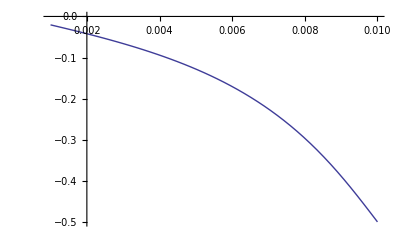

```mathematica
Plot[
MagnetCoilForce[magnet,coil,  Displacement->x],
{x,1mm,10mm}]
```